```mathematica
VertexNames[n_]:=Table[k->Symbol[MyLetter[k]],{k,n}]
```

```mathematica
VertexNames[10]
```

{1→a,2→b,3→c,4→d,5→e,6→f,7→g,8→h,9→i,10→j}

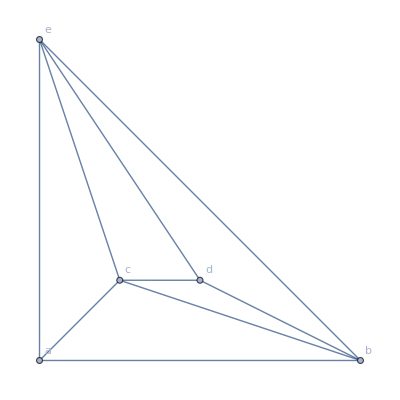
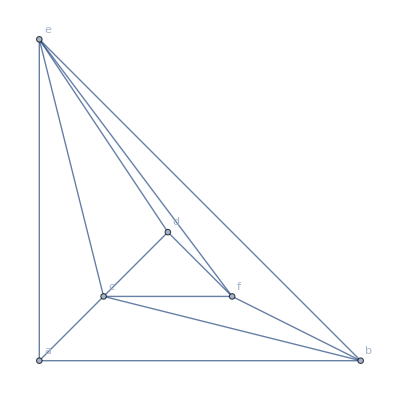
18 a-5 a b-3 a c+(-a+a b) c-6 a d+b (-a+a d)+2 c (-a+a d)+a (-b+b d)-b (2 a-a c-a d+c (-a+a d))-4 a e+c (-a+a e)+a (-b+b e)+2 a (-d+d e)-b (2 a-a d-a e+a (-d+d e))-a (2 c-c d-c e+c (-d+d e))+a (-6 b+2 b c+2 b d-c (-b+b d)+2 b e-c (-b+b e)-b (-d+d e)+b (2 c-c d-c e+c (-d+d e)))1
(-3+x)^2 (-2+x) (-1+x) x0
-Graphics-
-54 a+10 a b+8 a c-a (-b+b c)+22 a d-b (-a+a d)-c (-a+a d)-4 a (-b+b d)-2 a (-c+c d)+c (2 a-a b-a d+a (-b+b d))+2 a e-(-a+a b) e-(-a+a c) e-4 (-a+a d) e+c (2 a-2 a d+(-a+a d) e)+a (2 b-2 b d+(-b+b d) e)+12 a f-b (-a+a f)-2 e (-a+a f)-a (-b+b f)-2 a (-c+c f)-6 a (-d+d f)+b (2 a-a d-a f+a (-d+d f))+2 c (2 a-a d-a f+a (-d+d f))+a (2 b-b d-b f+b (-d+d f))+2 a (2 d-d e-d f+e (-d+d f))-b (-6 a+2 a c+2 a d-a (-c+c d)+2 a f-a (-c+c f)-a (-d+d f)+c (2 a-a d-a f+a (-d+d f)))-b (-6 a+3 a d+a e-(-a+a d) e+2 a f-e (-a+a f)-a (-d+d f)+a (2 d-d e-d f+e (-d+d f)))-a (-6 c+3 c d+c e-(-c+c d) e+2 c f-e (-c+c f)-c (-d+d f)+c (2 d-d e-d f+e (-d+d f)))+a (18 b-5 b c-8 b d+c (-b+b d)+b (-c+c d)-b e+(-b+b c) e+2 (-b+b d) e-c (2 b-2 b d+(-b+b d) e)-4 b f+e (-b+b f)+b (-c+c f)+2 b (-d+d f)-c (2 b-b d-b f+b (-d+d f))-b (2 d-d e-d f+e (-d+d f))+b (-6 c+3 c d+c e-(-c+c d) e+2 c f-e (-c+c f)-c (-d+d f)+c (2 d-d e-d f+e (-d+d f))))1
(-3+x)^3 (-2+x) (-1+x) x0
-Graphics-

```mathematica
Monitor[TableForm[
Table[With[{g=ReadGrof[k]},Framed[Column[{Pane[Labeled[Style[CalculateInOutFormulaAll[g],LineIndent->0,TextAlignment->Left],Style[ChromaticPolynomial[g,4]/24,Red,Bold]],500],
Pane[Labeled[Style[Factor[ChromaticPolynomial[g,x]],LineIndent->0,TextAlignment->Left],Style[ChromaticPolynomial[g,3],Red,Bold]],500],Graph[g,GraphLayout->"PlanarEmbedding",VertexLabels->VertexNames[VertexCount[g]]]}]]],{k,2,3}]
],k]
```

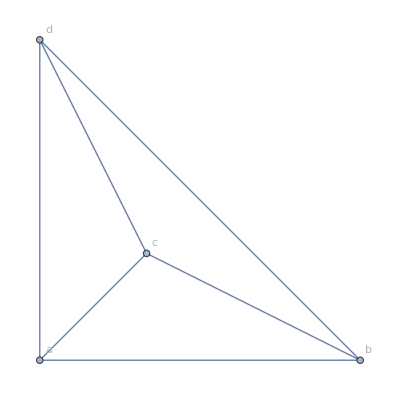
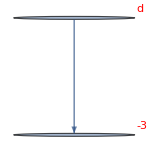
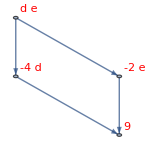
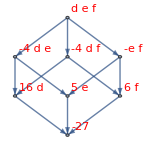
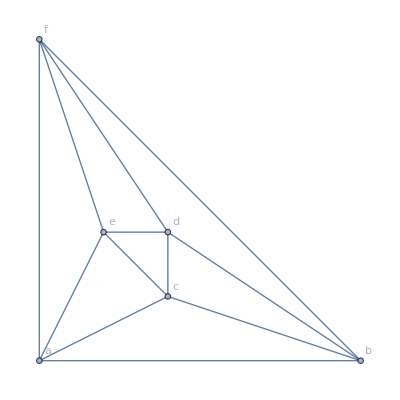
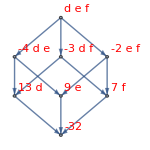
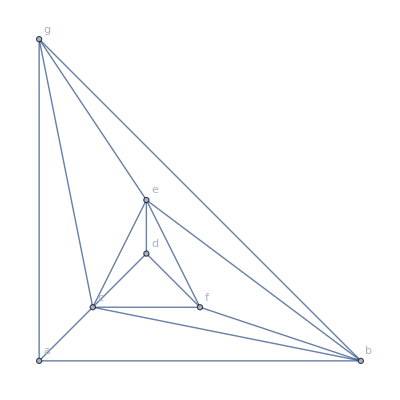
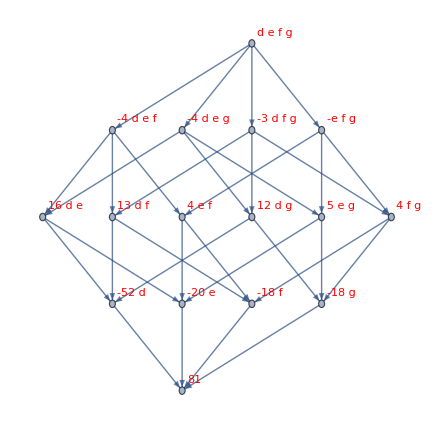
a (-1+b) (-2+c) (-3+d)1
(-3+x) (-2+x) (-1+x) x0
-Graphics-
-Graphics-
a (-1+b) (-2+c) (9-4 d-2 e+d e)1
(-3+x)^2 (-2+x) (-1+x) x0
-Graphics-
-Graphics-
a (-1+b) (-2+c) (-27+16 d+5 e-4 d e+6 f-4 d f-e f+d e f)1
(-3+x)^3 (-2+x) (-1+x) x0
-Graphics-
-Graphics-
a (-1+b) (-2+c) (-32+13 d+9 e-4 d e+7 f-3 d f-2 e f+d e f)4
(-2+x) (-1+x) x (-32+29 x-9 x^2+x^3)6
-Graphics-
-Graphics-
a (-1+b) (-2+c) (81-52 d-20 e+16 d e-18 f+13 d f+4 e f-4 d e f-18 g+12 d g+5 e g-4 d e g+4 f g-3 d f g-e f g+d e f g)1
(-3+x)^4 (-2+x) (-1+x) x0
-Graphics-
-Graphics-

```mathematica
Monitor[TableForm[
Table[With[{g=ReadGrof[k]},With[{form=Factor[CalculateInOutFormulaAll[g]]},Framed[Column[{Pane[Labeled[Style[form,LineIndent->0,TextAlignment->Left],Style[ChromaticPolynomial[g,4]/24,Red,Bold]],500],
Pane[Labeled[Style[Factor[ChromaticPolynomial[g,x]],LineIndent->0,TextAlignment->Left],Style[ChromaticPolynomial[g,3],Red,Bold]],500],Graph[g,GraphLayout->"PlanarEmbedding",VertexLabels->VertexNames[VertexCount[g]]],
ExpressionLattice[Expand[form/(a(-1+b) (-2+c))]]
}
]]]],{k,5}]
],k]
```

```mathematica
Association[]
```

<||>

```mathematica
IdempAssoc[Range[5]]
```

<|1→1,2→2,3→3,4→4,5→5|>

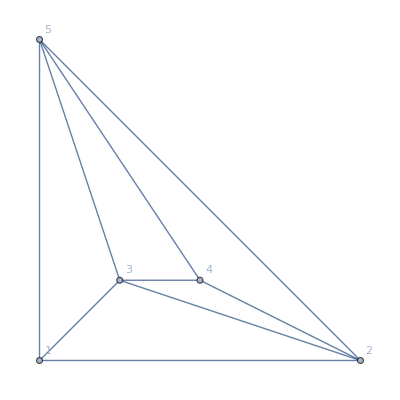

```mathematica
Graph[ReadGrof[2],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

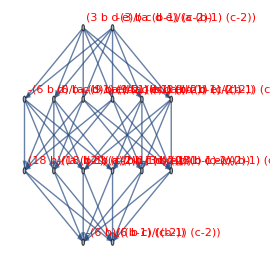
(-3+a) b (-1+c) (-3+d) (-2+e)1
(-3+x)^2 (-2+x) (-1+x) x0
-Graphics-
-Graphics-

```mathematica
With[{g=ReadGrof[2]},With[{form=Factor[CalculateInOutFormulaAll[g,VertexList[g],IdempAssoc[VertexList[g]],<|2->1,3->2,5->3,4->4,1->5|>]]},Framed[Column[{Pane[Labeled[Style[form,LineIndent->0,TextAlignment->Left],Style[ChromaticPolynomial[g,4]/24,Red,Bold]],500],
Pane[Labeled[Style[Factor[ChromaticPolynomial[g,x]],LineIndent->0,TextAlignment->Left],Style[ChromaticPolynomial[g,3],Red,Bold]],500],Graph[g,GraphLayout->"PlanarEmbedding",VertexLabels->VertexNames[VertexCount[g]]],
ExpressionLattice[Expand[form]]
}
]]]]
```

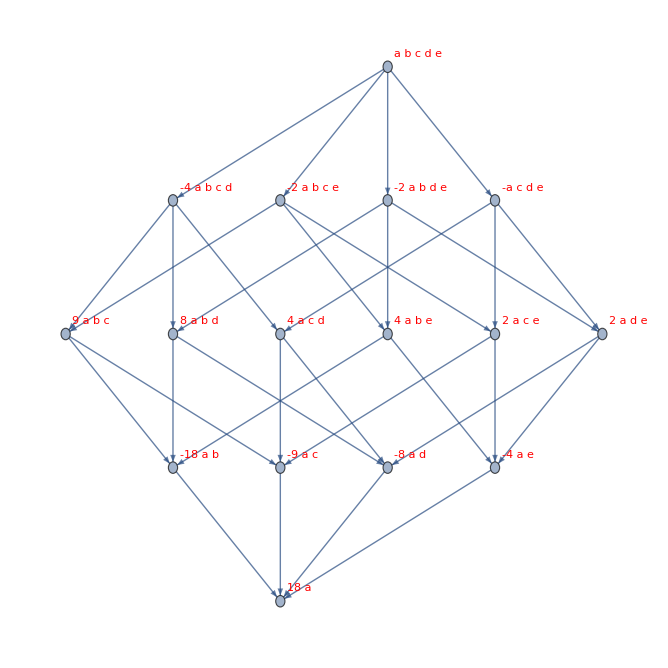
a (-1+b) (-2+c) (9-4 d-2 e+d e)1
(-3+x)^2 (-2+x) (-1+x) x0
-Graphics-
-Graphics-

```mathematica
With[{g=ReadGrof[2]},With[{form=Factor[CalculateInOutFormulaAll[g,VertexList[g],IdempAssoc[VertexList[g]]]]},Framed[Column[{Pane[Labeled[Style[form,LineIndent->0,TextAlignment->Left],Style[ChromaticPolynomial[g,4]/24,Red,Bold]],500],
Pane[Labeled[Style[Factor[ChromaticPolynomial[g,x]],LineIndent->0,TextAlignment->Left],Style[ChromaticPolynomial[g,3],Red,Bold]],500],Graph[g,GraphLayout->"PlanarEmbedding",VertexLabels->VertexNames[VertexCount[g]]],
ExpressionLattice[Expand[form]]
}
]]]]
```